MAT120        Assignment 2

5.  a)

```mathematica
plot1=ContourPlot[{x==1-y^2,x==y^2-1},{x,-2,3},{y,-2,2},Axes->True,AxesLabel->Automatic,PlotLegends->"Expressions"];
region1=ImplicitRegion[x>y^2-1&&x<1-y^2,{x,y}];
Show[plot1,RegionPlot[region1]]
```

-Graphics-

```mathematica
Area[region1]
```

8/3

Area of the bounded region  =  8/3 unit^2

b) 
L = ∫_a^b √(1+(dy/dx)^2)ⅆx  or   L = ∫_a^b √(1+(dx/dy)^2)ⅆy

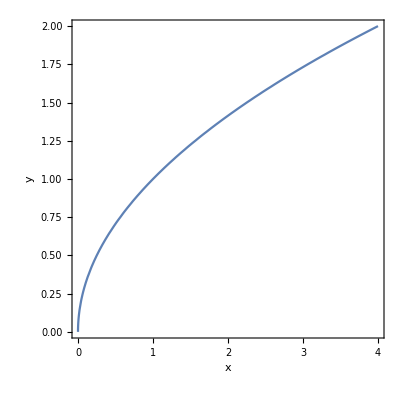

```mathematica
ContourPlot[x==y^2,{x,0,4},{y,0,2},Axes->True,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Solve[X==2^2,X,Reals]//N
```

{{X→4.}}

```mathematica
D[√X,X]
```

1/(2 √X)

```mathematica
L=∫_0^4 √(1+(1/(2 √X))^2)ⅆX//N
```

4.64678

The arc length of the curve = 4.64678 unit

c) Surface area by rotating curve about x-axis=∫_a^b 2πyⅆs
		  Surface area by rotating curve about y-axis=∫_a^b 2πxⅆs
ds=∫_a^b √(1+(dy/dx)^2)ⅆx   or ds=∫_a^b √(1+(dx/dy)^2)ⅆy

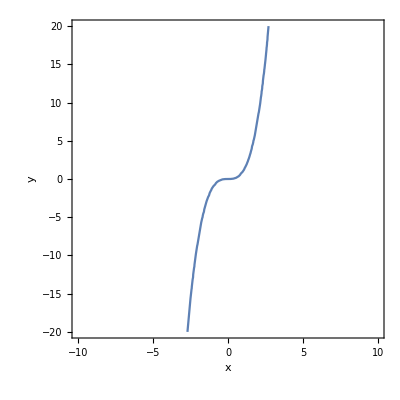

```mathematica
ContourPlot[x^3==y,{x,-10,10},{y,-20,20},Axes->True,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Solve[x^3==8,x,Reals]//N
```

{{x→2.}}

```mathematica
D[x^3,x]
```

3 x^2

```mathematica
s1=2π∫_0^2 x^3 √((3 x^2)^2+1)ⅆx//N
```

203.044

```mathematica
Surface area by rotating curve about x-axis=203.044 unit^2
```

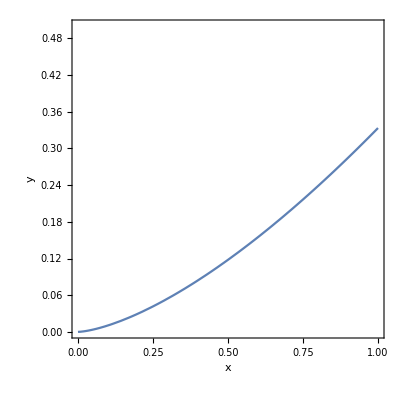

```mathematica
ContourPlot[3y==x^(3/2),{x,0,1},{y,0,0.5},Axes->True,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Solve[(3y)^(2/3)==1,y,Reals]//N
```

{{y→0.333333}}

```mathematica
D[(3y)^(2/3),y]
```

2/(3^(1/3) y^(1/3))

```mathematica
s2=2π∫_0^0.3333333333333333 (3y)^(2/3)√((2/(3^(1/3) y^(1/3)))^2+1)ⅆy//N
```

3.39221

Set::write: Tag Plus in -axis+about area by curve rotating Surface y is Protected.

3.39221 unit^2

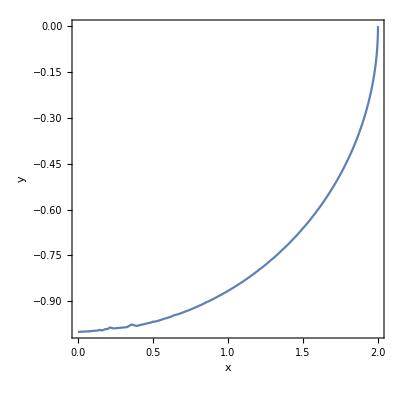

```mathematica
Surface area by rotating curve about y-axis=3.39221 unit^2




ContourPlot[x==2 √(1-y^2),{x,0,2},{y,-1,0},Axes->True,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Solve[2 √(1-y^2)==0,y,Reals]//N
```

{{y→-1.},{y→1.}}

```mathematica
D[2 √(1-y^2),y]
```

-(2 y)/(√(1-y^2))

```mathematica
s2=2π∫_-1^0 2 √(1-y^2)√((-(2 y)/(√(1-y^2)))^2+1)ⅆy//N
```

17.3438